```mathematica
Input["f[x_]:="];
Input["error, e="];
Input["initial guess, a="]
g[x_]=D[f[x], x];
h[x_]=D[g[x], x];
Do[b=a-(g[a]/h[a]); Print[N[b]];If[Abs[b-a]>e,a=b],{15}]
```

3

65.+a

65.+a

65.+a

«12 more identical outputs»

```mathematica
f[x_]=.65 ⅇ^(-(.01/.65)x)
```

0.65 ⅇ^(-0.0153846 x)

```mathematica
g[x_]=.65 ⅇ^(-(.01/.65)x)(200+5x)-.45x
```

-0.45 x+0.65 ⅇ^(-0.0153846 x) (200+5 x)

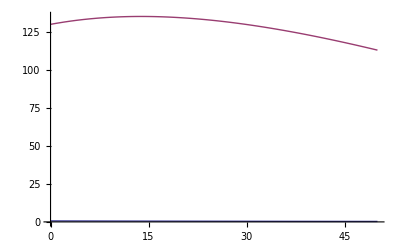

```mathematica
Plot[{f[x], g[x]}, {x,0,50}]
```